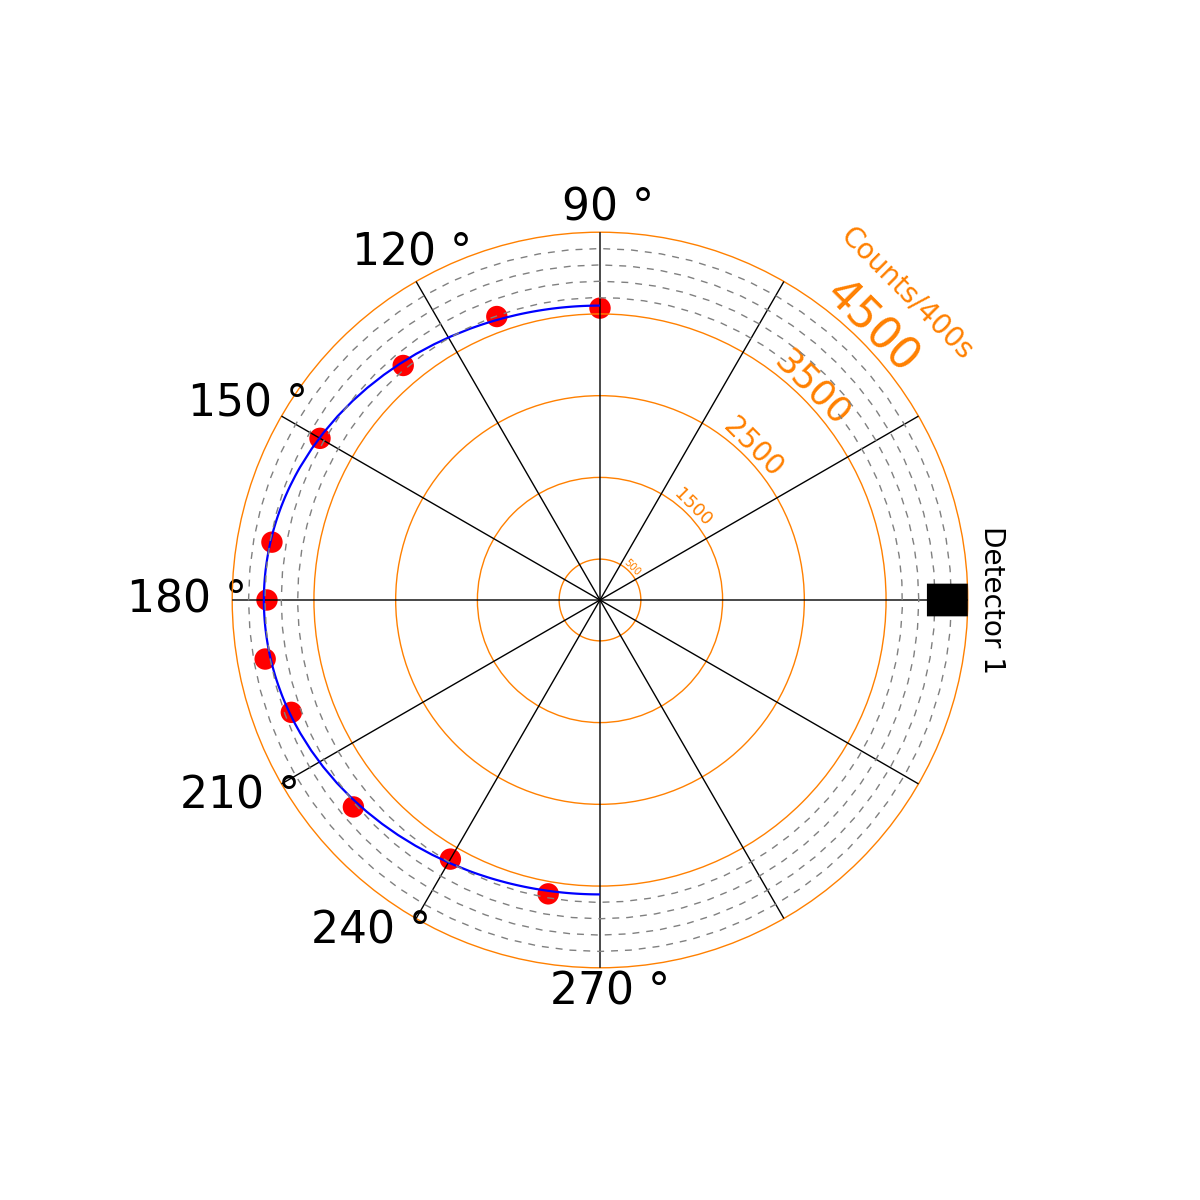

```mathematica
data = {{90, 3571.19},{110,3690.86},{130,3745.86},{150,3955.86},{170,4075.86},{180,4074.53},{200,4018.86},{220,3938.86},{240,3660.86},{260,3650.86},{190,4159.86}};
datapolar = Map[{#[[1]]*Pi/180,#[[2]] }&, data];
Show[ListPolarPlot[datapolar,PlotStyle->{Red}],Graphics[{Orange,Circle[{0,0},3500]}],Graphics[{Orange,Circle[{0,0},4500]}],Graphics[{Orange,Circle[{0,0},2500]}],Graphics[{Orange,Circle[{0,0},1500]}],Graphics[{Orange,Circle[{0,0},500]}],Graphics[Line[{{-3897,2250},{3897,-2250}}]],
Graphics[Line[{{-2250,3897},{2250,-3897}}]],
Graphics[Line[{{3897,2250},{-3897,-2250}}]],
Graphics[Line[{{2250,3897},{-2250,-3897}}]],
Graphics[Line[{{-4500,0},{4500,0}}]],
Graphics[Line[{{0,-4500},{0,4500}}]],
PolarPlot[3602.06*(1+0.1195*0.9623^2*Cos[x]^2+0.0403*0.8782^2*Cos[x]^4),{x,Pi/2,3*Pi/2},PlotStyle->Blue],
Plot[0,{x,-6000,6000},PlotStyle->Transparent],
Plot[6000,{x,-1,1},PlotStyle->Transparent],
Plot[-6000,{x,-1,1},PlotStyle->Transparent],
Graphics[Text[Style[90°,FontSize->44],{100,4800}]],
Graphics[Text[Rotate[Style[120°,FontSize->44],0],{-2300,4250}]],
Graphics[Text[Rotate[Style[150°,FontSize->44],0],{-4300,2400}]],
Graphics[Text[Rotate[Style[180°,FontSize->44],0],{-5050,0}]],
Graphics[Text[Rotate[Style[210°,FontSize->44],0],{-4400,-2400}]],
Graphics[Text[Rotate[Style[240°,FontSize->44],0],{-2800,-4050}]],
Graphics[Text[Style[270°,FontSize->44],{122,-4800}]],
Graphics[Text[Rotate[Style["Counts/400s",FontSize->28, Orange],-Pi/4],{3750,3750}]],
Graphics[Text[Rotate[Style[4500,FontSize->44, Orange],-Pi/4],{3330,3330}]],
Graphics[Text[Rotate[Style[3500,FontSize->36, Orange],-Pi/4],{2600,2600}]],
Graphics[Text[Rotate[Style[2500,FontSize->28, Orange],-Pi/4],{1870,1870}]],Graphics[Text[Rotate[Style[1500,FontSize->18, Orange],-Pi/4],{1130,1130}]],
Graphics[Text[Rotate[Style[500,FontSize->10, Orange],-Pi/4],{395,395}]],
Graphics[Text[Rotate[ Style["Detector 1",FontSize->28],-Pi/2],{4800,0}]],
Graphics[{Gray,Dashed,Circle[{0,0},3700,{52*Pi/180,2*Pi+38*Pi/180}]}],
Graphics[{Gray,Dashed,Circle[{0,0},3900]}],
Graphics[{Gray,Dashed,Circle[{0,0},4100]}],
Graphics[{Gray,Dashed,Circle[{0,0},4300]}],
Graphics[{Black,Rectangle[{4000,-200},{4500,200}]}],
Axes->False,
ImageSize->{1200,1200}
]
```